# Rapport projekt 31

Murtadha Alobadi, IX1307, mhaao@kth.se
Parosh Shaways, IX1307, shaways@kth.se

Uppgift 1: Trafikflöde

## Sammanfattning

### Uppgift

a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
b) Vilka andra förenklingar har vi antagit?

x) Ställ upp ekvationssystemet.
c) Bestäm trafikflödet för vägsystemet.
d) Om trafikflödet för en av x, y, z eller w begränsas till 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

### Resultat

a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
“Trafikflödet bevaras i varje korsning.” ett fordon som når en korsning måste fortsätta genom trafiksystemet. När det är ingen trafik och inget händer då är antagandet giltigt, alltså att trafikflödet bevaras. Den är felaktig då  flödet stannar av någon orsak. t.ex att en bil hamnar i en bilolycka  eller något annat händer på vägen så att trafiken stoppas.

b) Vilka andra förenklingar har vi antagit?
Ett positivt värde på flödet flyter i pilens riktning och ett negativt flöde flyter i motsatt riktning. Pilarna på själva ritningen är dessutom en förenkling. 

x) Ställ upp ekvationssystemet.
A-korsning
x+w=431  
Atonsu-Prempeh Rd  +  Roman Hill Road= 190 + 241 
B-korsning
x+y=255 
Atonsu-Prempeh Rd +  Labour-Asafo interct=150+105
C-korsning
z+y=340
Asafo market-Kaietia Rd +  Labour-Asafo interct=110+230
D-korsning
w+z=516
Roman Hill Road +  Asafo market-Kaietia Rd=280+236

c) Bestäm trafikflödet för vägsystemet.
Vi ta alla ekvationssystemet och med hjälp av Reduce vi få y,z,w och x-värde kan vara vad som helst då det inte är ett fast värde.

d) Om trafikflödet för en av x, y, z eller w begränsas till 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna? 
Vi har begränsade värde på 100 fordon/timme. Med hjälp av Reduce och den begränsade värde för trafikflödet för x,y,z och w vi få svar på vad blir trafikflödet för de andra vägarna är:

x=100 då är x=100, y=155, z=185 och w=331
y=100 då är x=155,  y=100, z==240 och w==276
z=100 då är x=15, y=240, z=100 och w==416
w=100 då är x==331, y=-76, z==416 och w==100

Vi ser att det går att begränsa alla värderna på alla väger förutom om w=100 då får vi negativt värde på y vägen och bilen går då motsatt håll vilket inte är möjligt i detta fall.

## Modell

### Modell för trafikflöde

figur 1. Diagram av vägsystem i Kumasi, Ghana (efter Adu et al. [2014])

## Kod

x) Ställ upp ekvationssystemet.

A)

```mathematica
x+w=431
```

B)

```mathematica
x+y=255
```

C)

```mathematica
z+y=340
```

D)

```mathematica
w+z=516
```

```mathematica
c) Bestäm trafikflödet för vägsystemet.
```

```mathematica
Reduce[{x+w==431, x+y==255,z+y==340,w+z==516}, {x, y, z, w}]
```

y==255-x&&z==85+x&&w==431-x

d) Om trafikflödet för en av x, y, z eller w begränsas till 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

Om trafikflödet för x=100

```mathematica
Reduce[{x+w==431, x+y==255,z+y==340,w+z==516, x==100}, {x, y, z, w}]
```

x==100&&y==155&&z==185&&w==331

Om trafikflödet för  y=100

```mathematica
Reduce[{x+w==431, x+y==255,z+y==340,w+z==516, y==100}, {x, y, z, w}]
```

x==155&&y==100&&z==240&&w==276

Om trafikflödet för z=100

```mathematica
Reduce[{x+w==431, x+y==255,z+y==340,w+z==516, z==100}, {x, y, z, w}]
```

x==15&&y==240&&z==100&&w==416

Om trafikflödet för w=100

```mathematica
Reduce[{x+w==431, x+y==255,z+y==340,w+z==516, w==100}, {x, y, z, w}]
```

x==331&&y==-76&&z==416&&w==100

Uppgift 2: Kaniner

## Sammanfattning

### Uppgift

a) Beräkna talföljden och rita en graf över den.
b) Undersök talföljden och diskutera tillväxtakten.
c) Vilka begränsningar har modellen?
d) Hur kan man förbättra modellen?

### Resultat

a) Beräkna talföljden och rita en graf över den.

förökningen av kaniner från månad n=1 
p_n är antal kaniner vid månad
 Antal kaniner  p_(n+2)=p_(n+1)+p_n
 
 Då få vi ett differensekvation
 p_n=p_(n-1)+p_(n-2)

Mede hjälp av Table vi kan få värde på 24 månaden.
Med hjälp av ListPlot vi rita diagram som visar antal kaniner för varje månad.

b) Undersök talföljden och diskutera tillväxtakten.
Talföljden visar hur kaniner växer enligt exponential utveckling (exponentialfunktion). Till exempel inom 15 månader får man 610 kaniner. Från början ökar kaniner sakta men sedan ökar det i snabbare takt, detta eftersom flera kaniner kan då para sig och föröka sig.

c) Vilka begränsningar har modellen?
I Modellen kan man inte veta värdena mellan punkterna, dvs bara se varje månad och inte för varje dag. En linje i modellen kanske hade hjälp då ser man ungefär relativt vilket värde som finns i en viss punkt mellan månadspunkterna.  Första punkter gör det inte särkilt tydligt vilka värden de har då de alla snuddar x-axeln.

d) Hur kan man förbättra modellen?
Om vi vill förbättra modellen behöver man då ändra hela differensekvationen och få fram ny modell. Just nu är det som sagt många punkter på X-axeln och man blir lite förvirrad vilka värden de har. Att öka Y eller X axelns värde hade förvärrat det visuellt. Man kan genom en linje se lutningen på hur den stiger. då får man bättre förrutsättningar till att undersöka värdena.

## Modell

### Modell för trafikflöde

Antal kaniner per månad

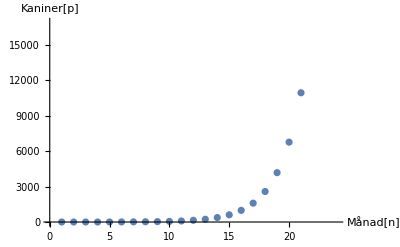

## Kod

```mathematica
p[1]=1
p[2]=1
p[n_]:=p[n-1]+p[n-2]
```

1

1

```mathematica
Antalkaniner=Ptotal=Table[p[n], {n, 1, 24}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368}

```mathematica
ListPlot[Antalkaniner,AxesLabel->{"Månad[n]","Kaniner[p]"}]
```

-Graphics-